***** Warning ! *****
BaseIO: redefining field speed.
********************
Field arrayOrdering defaults to RowMajor
Field origin defaults to {0,0}
Field order defaults to 1
Field spreadSeeds defaults to -1
Field showProgress defaults to 0
Field factoringMethod defaults to None
Fast marching solver completed in 6.2e-05 s.
Field exportActiveNeighs defaults to 0
Field exportGeodesicFlow defaults to 0
Unused fields from compute : FMCPUTime MaxStencilWidth StencilCPUTime nAccepted values 
Defaulted fields : arrayOrdering exportActiveNeighs exportGeodesicFlow factoringMethod order origin refineStencilAtWallBoundary showProgress spreadSeeds

{False,True}

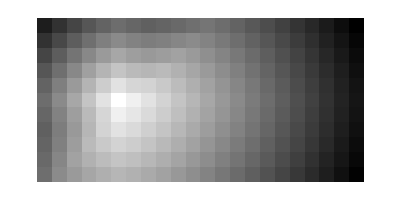

```mathematica
Module[{params=Association[{}],n=11,values,test,used,defaulted,modelName},
modelName = "Isotropic2";
hfmLibraryPath=FileNameJoin[{hfmBinDirectory,"libMathematicaHFM_"<>modelName}]; 
params["speed"]=Array[1.&,{2n,n}];
params["dims"]={2n,n};
params["gridScale"]=1./n;
params["seeds"]={{0.5,0.5}};
params["exportValues"]=1.;

LoadHFMWLL[hfmLibraryPath];
hfmSetVariable[#1,#2]&@@@Normal[params];
hfmSetVariable["speed",Array[If[#1>#2,2.,1.]&,{2n,n}]];
hfmSetVariable["verbosity",2];
hfmRunModel[];
values=hfmGetArray[2]["values"];
Print[hfmHasField/@{"Hi","MaxStencilWidth"}];
hfmEraseField["FMCPUTime"];
UnloadHFMWLL[];
TablePlot[values]
]
```